```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-10-28"}];
laptop=FileNameJoin[{"/","home","karl"}];
labComp=FileNameJoin[{"C:","Users","kahrendsen2"}];
dropboxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns","18-01-03_PolarizingElectrons"}];
folder=FileNameJoin[{labComp,dropboxOn}];
SetDirectory[folder];
files=FileNames["*.dat"]
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large];

plotLabel="Plot Label";
yAxisLabel="Y";
xAxisLabel="X";
ps={LabelStyle->18,PlotLabel->plotLabel,AxesLabel->{xAxisLabel,yAxisLabel}}
```

{EX2018-01-03_112039.dat,part1PumpScan.dat,part2PumpScan.dat}

{LabelStyle→18,PlotLabel→Plot Label,AxesLabel→{X,Y}}

```mathematica
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];


headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
```

<|#Filename:→/home/pi/RbData/2018-01-03/EX2018-01-03_112039.dat,#USB1208->HP3617Aconversion:→0.030938,#FilamentBias:→-100.1,#NumberOfSecondsPerCountMeasurement:→3,#Comments:→Excitation,#IonGauge(Torr):→0.000093,#CVGauge(N2)(Torr):→0.102,#CVGauge(He)(Torr):→0.00105,#CellTemp(Res):→50.4,#CellTemp(Targ):→110.,#MagnitudeOfCurrent(*10^-X):→8|>

Dataset[<>]

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Failure[{MessageTemplate:>Dataset::partmismatch,MessageParameters→<|Type→TypeSystem`Struct[{Aout,bias,N2Offset,N2Sweep,TotalHeOffset,PrimaryElectronEnergy,SecondaryElectronEnergy,Count,CountStDev,Current,CurrentStDev,IonGauge,IGStdDev},{TypeSystem`Atom[Integer],TypeSystem`Atom[Real],«9»,TypeSystem`Atom[Real],TypeSystem`Atom[Real]}],Part→«8»,Symbol→Part|>},«7»]].

{15.2496,15.4352,15.6208,15.8064,15.9921,16.1777,16.3633,16.549,16.7346,16.9202,17.1059,17.2915,17.4771,17.6628,17.8484,18.034,18.2196,18.4053,18.5909,18.7765,18.9622,19.1478,19.3334,19.5191,19.7047,19.8903,20.076,20.2616,20.4472,20.6328,20.8185,21.0041,21.1897,21.3754,21.561,21.7466,21.9323,22.1179,22.3035,22.4891,22.6748,22.8604,23.046,23.2317,23.4173,23.6029,23.7886,23.9742,24.1598,24.3455,24.5311,24.7167,24.9023,25.088,25.2736,25.4592,25.6449,25.8305,26.0161,26.2018,26.3874,26.573,26.7586,26.9443,27.1299,27.3155,27.5012,27.6868,27.8724,28.0581,28.2437,28.4293,28.615,28.8006,28.9862,29.1718,29.3575,29.5431,29.7287,29.9144}

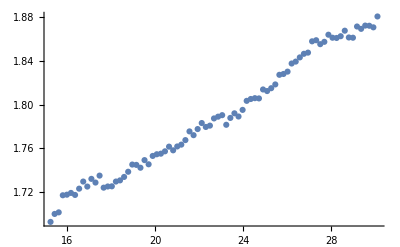

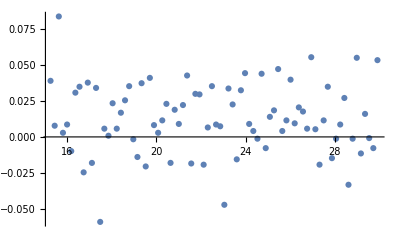

Transpose::nmtx: The first two levels of {{15.2496,15.4352,15.6208,15.8064,15.9921,16.1777,16.3633,16.549,16.7346,16.9202,17.1059,17.2915,17.4771,17.6628,17.8484,18.034,18.2196,18.4053,18.5909,18.7765,18.9622,19.1478,«7»,20.6328,20.8185,21.0041,21.1897,21.3754,21.561,21.7466,21.9323,22.1179,22.3035,22.4891,22.6748,22.8604,23.046,23.2317,23.4173,23.6029,23.7886,23.9742,24.1598,24.3455,«31»},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{15.2496,15.4352,15.6208,15.8064,15.9921,16.1777,16.3633,16.549,16.7346,16.9202,17.1059,17.2915,17.4771,17.6628,17.8484,18.034,18.2196,18.4053,18.5909,18.7765,18.9622,19.1478,«8»,20.8185,21.0041,21.1897,21.3754,21.561,21.7466,21.9323,22.1179,22.3035,22.4891,22.6748,22.8604,23.046,23.2317,23.4173,23.6029,23.7886,23.9742,24.1598,24.3455,«31»},«7»[«1»]}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{15.2496,15.4352,15.6208,15.8064,15.9921,16.1777,16.3633,16.549,16.7346,16.9202,17.1059,17.2915,17.4771,17.6628,17.8484,18.034,18.2196,18.4053,18.5909,18.7765,18.9622,19.1478,19.3334,19.5191,19.7047,19.8903,20.076,20.2616,20.4472,20.6328,20.8185,21.0041,21.1897,21.3754,21.561,21.7466,21.9323,22.1179,22.3035,22.4891,22.6748,22.8604,23.046,23.2317,23.4173,23.6029,23.7886,23.9742,24.1598,24.3455,24.5311,24.7167,24.9023,25.088,25.2736,25.4592,25.6449,25.8305,26.0161,26.2018,26.3874,26.573,26.7586,26.9443,27.1299,27.3155,27.5012,27.6868,27.8724,28.0581,28.2437,28.4293,28.615,28.8006,28.9862,29.1718,29.3575,29.5431,29.7287,29.9144,30.1},Failure[{MessageTemplate:>Dataset::partmismatch,MessageParameters→<|Type→TypeSystem`Struct[{Aout,bias,N2Offset,N2Sweep,TotalHeOffset,PrimaryElectronEnergy,SecondaryElectronEnergy,Count,CountStDev,Current,CurrentStDev,IonGauge,IGStdDev},{TypeSystem`Atom[Integer],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Integer],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real]}],Part→Counts,Symbol→Part|>},Dataset]}]]

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Failure[{MessageTemplate:>Dataset::partmismatch,MessageParameters→<|Type→TypeSystem`Struct[{Aout,bias,N2Offset,N2Sweep,TotalHeOffset,PrimaryElectronEnergy,SecondaryElectronEnergy,Count,CountStDev,Current,CurrentStDev,IonGauge,IGStdDev},{TypeSystem`Atom[Integer],TypeSystem`Atom[Real],«9»,TypeSystem`Atom[Real],TypeSystem`Atom[Real]}],Part→«8»,Symbol→Part|>},«7»]].

General::stop: Further output of Differences::listrp will be suppressed during this calculation.

-Graphics-

{ImageSize→Large,PlotLabel→Retarding Field Analysis,AxesLabel→{Electron Energy (eV),d(Counts)/d(Energy)}}

FittedModel[72.3887 ⅇ^(-0.0235328 (-«18»+x)^2)]

72.3887 ⅇ^(-0.0235328 (-54.7933+x)^2)

{ampl→836.39,m→54.7933,σ→4.60944}

{8.80511×10^8,1.69257×10^6,152330.}

-5

418.195

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

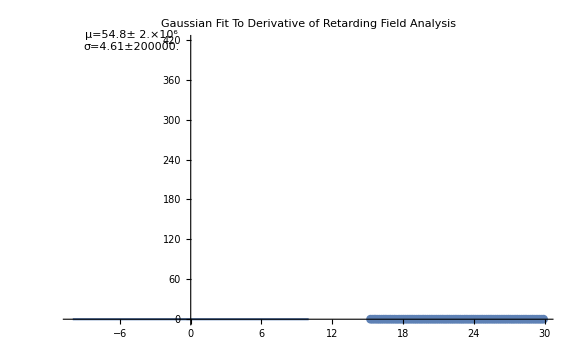

{/home/pi/RbData/2018-01-03/EX2018-01-03_112039.dat,0.102,2.,-100.1,54.7933,4.60944,mid[1,Current],mid[-1,Current],high[-1,Current]}

```mathematica
ClearAll;
timeMid=112039;
timeHigh=timeMid;
midFile=FileNames["*"<>ToString[timeMid]<>".dat"][[1]];
highFile=FileNames["*"<>ToString[timeHigh]<>".dat"][[1]];

header=GetFileHeaderInfo[highFile]
data=GetFileDataset[highFile]
energy=Reverse[Normal[data[All,"PrimaryElectronEnergy"]]];
current=Reverse[Normal[data[All,"Current"]]];
counts=Reverse[Normal[data[All,"Count"]]];
currentDiff=Differences[current];
energyDiff=Differences[energy];
countsDiff=Differences[counts];
energyOneRemoved=Take[energy,{1,-2}]
currentDer=currentDiff/energyDiff;
countsDer=countsDiff/energyDiff;
ListPlot[Transpose[{energy,current}]]
ListPlot[Transpose[{energyOneRemoved,currentDer}]]
ListPlot[Transpose[{energy,counts}]]
ListPlot[Transpose[{energyOneRemoved,countsDer}]]


plotTitle="Retarding Field Analysis";

data1=Transpose[{energy,current}];
data2=Transpose[{energyOneRemoved,currentDer}];

yAxisTitle="d(Counts)/d(Energy)";
xAxisTitle="Electron Energy (eV)";
dataLabel1="Data";
dataLabel2="Derivative";
ps={ImageSize->Large, PlotLabel->plotTitle,AxesLabel->{xAxisTitle,yAxisTitle}}

plotData=data2;
gaussModel[x_]=ampl Evaluate[PDF[NormalDistribution[m,σ],x]];
fit=NonlinearModelFit[plotData,gaussModel[x],{ampl,{m,0},σ},x]
model=Normal[fit]
pe=fit["BestFitParameters"] (*Parameter Estimates*)
errors=fit["ParameterErrors"]


x1=-5
y1=.5*(ampl)/.pe
fitInfo=StringForm["μ=``± ``\nσ=``±``",NumberForm[m/.pe,3],NumberForm[errors[[2]],1],NumberForm[σ/.pe,3],NumberForm[errors[[3]],1]];
Show[{Plot[gaussModel[x]/.pe,{x,-10,10},PlotRange->All,PlotLabel->"Gaussian Fit To Derivative\nof Retarding Field Analysis"],
Graphics[Text[fitInfo,{x1,y1}],BaseStyle->15],
ListPlot[plotData,PlotLabel->"PLOT2"]}]
bothPlot=ListPlot[{Legended[data2,dataLabel2],Legended[data1,dataLabel1]}];
derivativePlot=ListPlot[Legended[data2,dataLabel2],ps];
entry ={header["#Filename:"],header["#CVGauge(N2)(Torr):"],data[1,"N2Offset"],data[1,"bias"],m/.pe, σ/.pe,mid[1,"Current"],mid[-1,"Current"],high[-1,"Current"]}

Rasterize[bothPlot];
Rasterize[derivativePlot];
```

```mathematica
maxDerPos=Position[currentDer,Max[currentDer]][[1]];
energyOfPeak=energyOneRemoved[[maxDerPos]][[1]]
Clear[maxDerPos,energyOfPeak]
```

1.9042

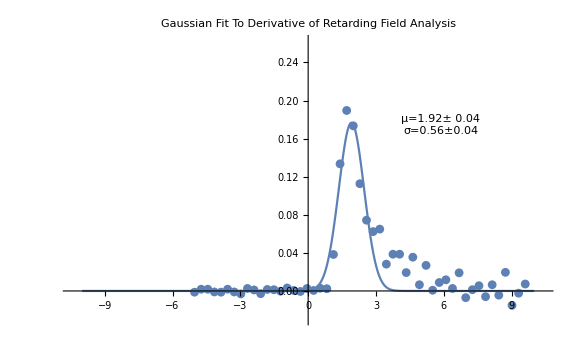

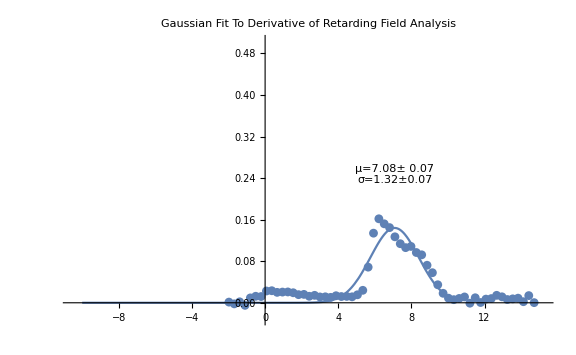

```mathematica
ExcitationFunctionProcessor[timeString_]:=Module[{file,ps,header,data,energy,energyDiff,current,currentDiff,energyOneRemoved,currentDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,x1,y1},
file=FileNames["*"<>ToString[timeString]<>".dat"][[1]];

header=GetFileHeaderInfo[file];
data=GetFileDataset[file];
energy=Reverse[Normal[data[All,"PrimaryElectronEnergy"]]];
current=Reverse[Normal[data[All,"Current"]]];
currentDiff=Differences[current];
energyDiff=Differences[energy];
energyOneRemoved=Take[energy,{1,-2}];
currentDer=currentDiff/energyDiff;
Print[ListPlot[Transpose[{energy,current}]]];
Print[ListPlot[Transpose[{energyOneRemoved,currentDer}]]];


plotTitle="Retarding Field Analysis";

plotData=Transpose[{energy,current}];
plotData2=Transpose[{energyOneRemoved,currentDer}];



(*
yAxisTitle="d(Counts)/d(Energy)";
xAxisTitle="Electron Energy (eV)";
dataLabel1="Data";
dataLabel2="Derivative";
*)
ps={ImageSize->Large, PlotLabel->plotTitle,AxesLabel->{"X","Y"}};

plotData=plotData2;
gaussModel[x_]=ampl Evaluate[PDF[NormalDistribution[m,σ],x]];
(*Find the position of the peak of the derivative data*)
maxDerPos=Position[currentDer,Max[currentDer]][[1]];
energyOfPeak=energyOneRemoved[[maxDerPos]][[1]];

fit=NonlinearModelFit[plotData,gaussModel[x],{ampl,{m,energyOfPeak},σ},x];
model=Normal[fit];
pe=fit["BestFitParameters"]; (*Parameter Estimates*)
errors=fit["ParameterErrors"];


x1=energyOfPeak-(3σ/.pe);
y1=.25*(ampl)/.pe;
fitInfo=StringForm["μ=``± ``\nσ=``±``",NumberForm[m/.pe,3],NumberForm[errors[[2]],1],NumberForm[σ/.pe,3],NumberForm[errors[[3]],1]];
Print[Show[{Plot[gaussModel[x]/.pe,{x,energyOfPeak-5,energyOfPeak+5},PlotRange->All,PlotLabel->"Gaussian Fit To Derivative\nof Retarding Field Analysis"],
Graphics[Text[fitInfo,{x1,y1}],BaseStyle->15],
ListPlot[plotData,PlotLabel->"PLOT2"]}]];
bothPlot=ListPlot[{Legended[data2,dataLabel2],Legended[data1,dataLabel1]}];
derivativePlot=ListPlot[Legended[data2,dataLabel2],ps];

entry ={header["#Filename:"],header["#CVGauge(N2)(Torr):"],data[1,"N2Offset"],data[1,"bias"],m/.pe, σ/.pe,current[[1]],current[[-1]]}
];
```

{144806,145539}

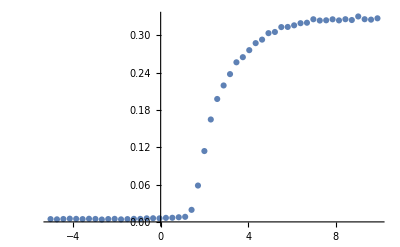

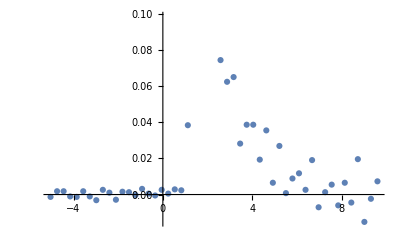

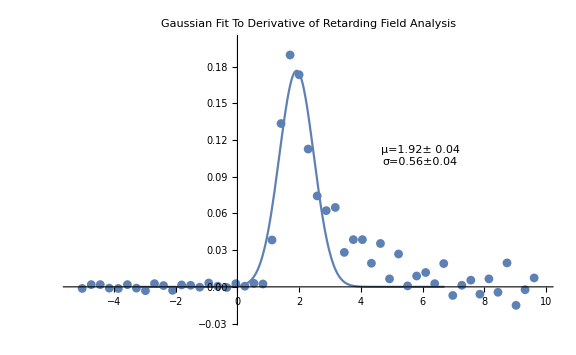

{/home/pi/RbData/2017-10-16/EX2017-10-16_144806.dat,0.133,2.,-30.,1.91544,0.559882,0.004504,0.327461}

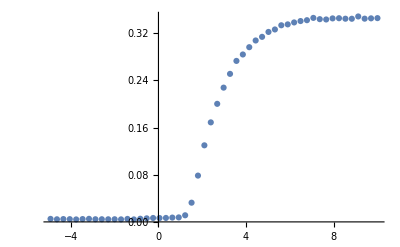

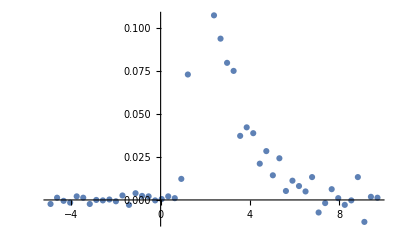

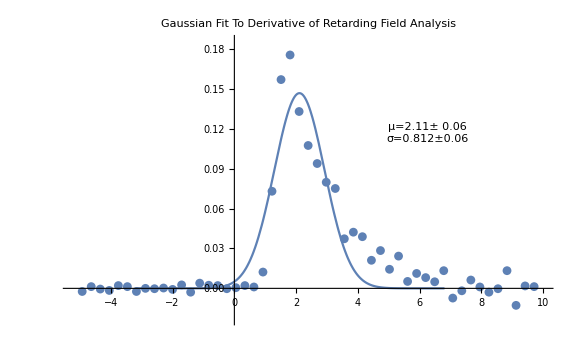

{/home/pi/RbData/2017-10-16/EX2017-10-16_145539.dat,0.133,2.,-30.,2.10764,0.811885,0.005114,0.345704}

```mathematica
one={141218,141507};
three={104205,104926};
four={152639,153359};
six={111030,111334};
nine={122609,122936};
ten={143028,144100};
twelve={092931,093614};
thirteen={151327,151641};
fifteen={113435,114518};
eighteen={120228,120529};
nineRerun={124147,125016};
tenRerun={144806,145539}
data=tenRerun;
run1=ExcitationFunctionProcessor[data[[1]]]
run2=ExcitationFunctionProcessor[data[[2]]]
```

```mathematica
aggregateData={}
```

{}

```mathematica
aggregateData=Append[aggregateData,run2]
```

```mathematica
aggregateData={{"/home/pi/RbData/2017-10-16/EX2017-10-16_141507.dat",0.0588,2.,-30.,2.238730867263941,0.9652159025047532,0.004885,0.828575},{"/home/pi/RbData/2017-10-16/EX2017-10-16_104926.dat",0.0637,7.9,-120.,1.533221446155136,2.3026610204624407,0.003893,0.49081},{"/home/pi/RbData/2017-10-16/EX2017-10-16_153359.dat",0.0637,27.1,-30.,0.6194853508057808,0.7042842441221938,0.004122,0.276166},{"/home/pi/RbData/2017-10-16/EX2017-10-16_111334.dat",0.0637,30.5,-120.,0.35084288608904907,1.1448561909515387,0.004046,0.432416},{"/home/pi/RbData/2017-10-16/EX2017-10-16_111030.dat",0.063,30.5,-120.,31.10406012233879,0.7886936719552535,0.439515,0.683851},{"/home/pi/RbData/2017-10-16/EX2017-10-16_122609.dat",0.0595,91.5,-120.,93.57352765309078,1.1371220004243419,0.391121,0.474856},{"/home/pi/RbData/2017-10-16/EX2017-10-16_122936.dat",0.0595,91.5,-120.,0.5959171581951423,1.2596350860067187,-0.001603,0.26403},{"/home/pi/RbData/2017-10-16/EX2017-10-16_144100.dat",0.133,2.,-30.,2.20453803113021,0.8552504468807877,0.003893,0.332957},{"/home/pi/RbData/2017-10-16/EX2017-10-16_093614.dat",0.162,5.7,-120.,7.080237014931026,1.3213784279049627,0.052898,0.623473},{"/home/pi/RbData/2017-10-16/EX2017-10-16_151641.dat",0.133,27.,-30.,0.4932115048609198,1.0401245554660628,0.630954,1.351978},{"/home/pi/RbData/2017-10-16/EX2017-10-16_113435.dat",0.133,30.5,-120.,30.742753406659293,1.8897718797575567,0.012595,0.151441},{"/home/pi/RbData/2017-10-16/EX2017-10-16_114518.dat",0.133,30.5,-120.,-0.2875805353124037,0.9156836337910712,0.643319,1.086346},{"/home/pi/RbData/2017-10-16/EX2017-10-16_120228.dat",0.133,91.5,-120.,91.13515141231895,2.845902244548347,0.902769,1.3561},{"/home/pi/RbData/2017-10-16/EX2017-10-16_120529.dat",0.133,91.5,-120.,0.7730862267866122,1.4529087037629216,0.059004,0.45066},{"/home/pi/RbData/2017-10-16/EX2017-10-16_124147.dat",0.0595,91.5,-120.,93.53449523960926,1.2403170974189666,0.357001,0.86094},{"/home/pi/RbData/2017-10-16/EX2017-10-16_125016.dat",0.0588,91.5,-120.,0.38309009562850205,1.0054107133111474,-0.002443,0.231207},{"/home/pi/RbData/2017-10-16/EX2017-10-16_144806.dat",0.133,2.,-30.,1.915438366828938,0.5598822701902231,0.004504,0.327461},{"/home/pi/RbData/2017-10-16/EX2017-10-16_145539.dat",0.133,2.,-30.,2.1076406383375366,0.8118853132206681,0.005114,0.345704}}
Export["electronGunAggregateData.csv",aggregateData,"CSV"]
```

{{/home/pi/RbData/2017-10-16/EX2017-10-16_141507.dat,0.0588,2.,-30.,2.23873,0.965216,0.004885,0.828575},{/home/pi/RbData/2017-10-16/EX2017-10-16_104926.dat,0.0637,7.9,-120.,1.53322,2.30266,0.003893,0.49081},{/home/pi/RbData/2017-10-16/EX2017-10-16_153359.dat,0.0637,27.1,-30.,0.619485,0.704284,0.004122,0.276166},{/home/pi/RbData/2017-10-16/EX2017-10-16_111334.dat,0.0637,30.5,-120.,0.350843,1.14486,0.004046,0.432416},{/home/pi/RbData/2017-10-16/EX2017-10-16_111030.dat,0.063,30.5,-120.,31.1041,0.788694,0.439515,0.683851},{/home/pi/RbData/2017-10-16/EX2017-10-16_122609.dat,0.0595,91.5,-120.,93.5735,1.13712,0.391121,0.474856},{/home/pi/RbData/2017-10-16/EX2017-10-16_122936.dat,0.0595,91.5,-120.,0.595917,1.25964,-0.001603,0.26403},{/home/pi/RbData/2017-10-16/EX2017-10-16_144100.dat,0.133,2.,-30.,2.20454,0.85525,0.003893,0.332957},{/home/pi/RbData/2017-10-16/EX2017-10-16_093614.dat,0.162,5.7,-120.,7.08024,1.32138,0.052898,0.623473},{/home/pi/RbData/2017-10-16/EX2017-10-16_151641.dat,0.133,27.,-30.,0.493212,1.04012,0.630954,1.35198},{/home/pi/RbData/2017-10-16/EX2017-10-16_113435.dat,0.133,30.5,-120.,30.7428,1.88977,0.012595,0.151441},{/home/pi/RbData/2017-10-16/EX2017-10-16_114518.dat,0.133,30.5,-120.,-0.287581,0.915684,0.643319,1.08635},{/home/pi/RbData/2017-10-16/EX2017-10-16_120228.dat,0.133,91.5,-120.,91.1352,2.8459,0.902769,1.3561},{/home/pi/RbData/2017-10-16/EX2017-10-16_120529.dat,0.133,91.5,-120.,0.773086,1.45291,0.059004,0.45066},{/home/pi/RbData/2017-10-16/EX2017-10-16_124147.dat,0.0595,91.5,-120.,93.5345,1.24032,0.357001,0.86094},{/home/pi/RbData/2017-10-16/EX2017-10-16_125016.dat,0.0588,91.5,-120.,0.38309,1.00541,-0.002443,0.231207},{/home/pi/RbData/2017-10-16/EX2017-10-16_144806.dat,0.133,2.,-30.,1.91544,0.559882,0.004504,0.327461},{/home/pi/RbData/2017-10-16/EX2017-10-16_145539.dat,0.133,2.,-30.,2.10764,0.811885,0.005114,0.345704}}

electronGunAggregateData.csv

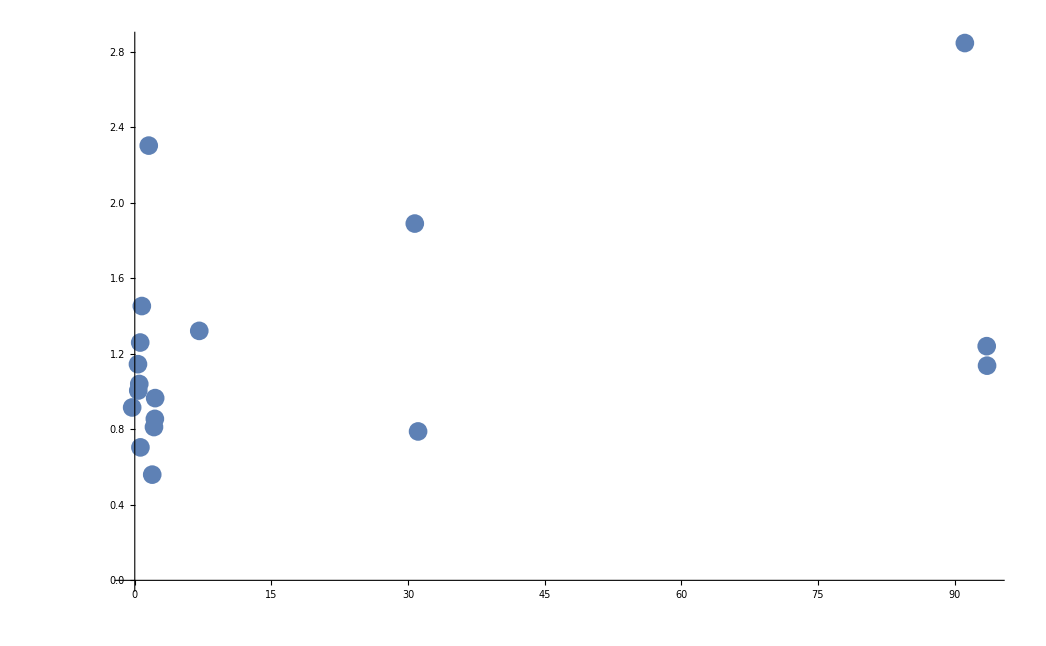

Dataset[<>]

Dataset[<>]

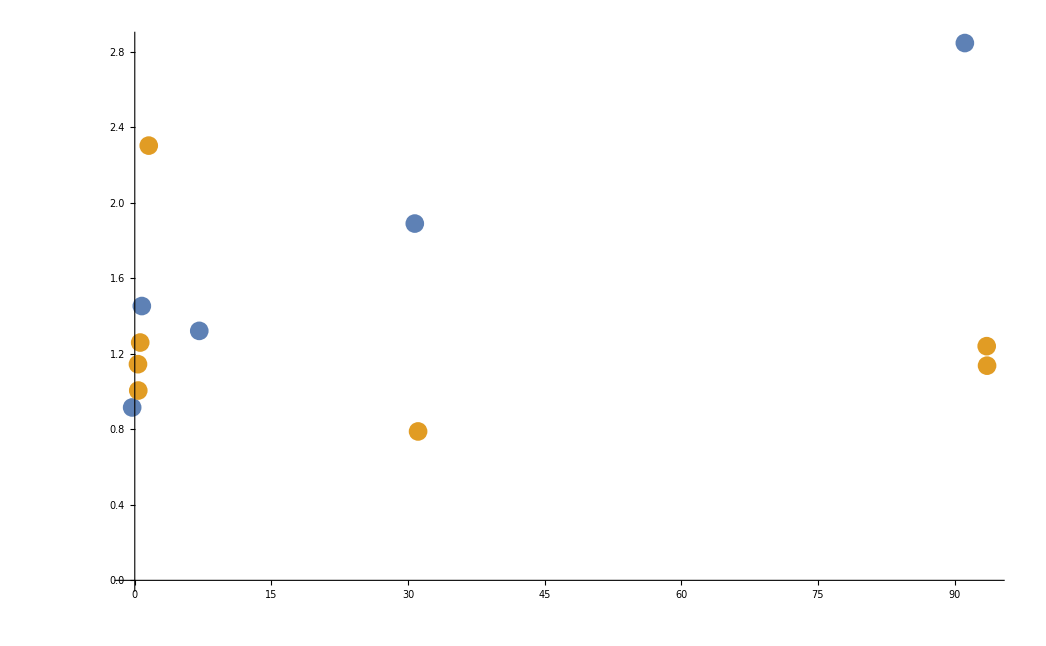

```mathematica
ds=Dataset[aggregateData];
electronEnergyVsBeamWidth=Normal[Take[ds,All,{5,6}]];
ListPlot[electronEnergyVsBeamWidth,PlotRange->{All,All}]
highPressure=Select[ds,#[[2]]>.09∧#[[4]]<-80&]
highPressurePlot=Take[highPressure,All,{5,6}];
lowPressure=ds[Select[#[[2]]<.09∧#[[4]]<-80&]]
lowPressurePlot=Take[lowPressure,All,{5,6}];
ListPlot[{highPressurePlot,lowPressurePlot},PlotRange->Full,PlotStyle->ps]

hpAndLowBias=Select[highPressure,#[[4]]>-80&];
hpAndHighBias=Select[highPressure,#[[4]]<-80&];
```